# Ring Oscillator

## using Hill Funtions

```mathematica
<<xlr8r.m
```

xlr8r 0.74 (13 May 2009) loaded 25 October 2009 at 09:29 GMT-06:60 using Mathematica 7.0 for Linux x86 (64-bit) (February 18, 2009) (Version 7., Release 1) (MathSBML 2.9.0 [8-Oct-2008])
GNU Lesser General Public License (LGPL) Terms Apply.

```mathematica
r={
{U↦V,hill[1,KH,-n,0, v]},
{V↦W,hill[1,KH,-n,0, v] }, 
{W↦U,hill[1,KH,-n,0, v] }, 
{V⇄ ∅,k1, k2}, {U⇄ ∅,k1, k2}, {W⇄∅,k1, k2}};
```

```mathematica
interpret[r]
```

{{U'[t]==k2-k1 U[t]+v/(1+KH^-n W[t]^n),V'[t]==k2+v/(1+KH^-n U[t]^n)-k1 V[t],W'[t]==k2+v/(1+KH^-n V[t]^n)-k1 W[t]},{U,V,W}}

```mathematica
baseic={U-> .9, V-> 1, W-> 1.1};
baserates={KH->1,v->2,k1->0.01,k2->0,n->3};
```

### Use Manipulate to explore parameter space

```mathematica
rplot[K_, vmax_, kin_, kout_, cooperativity_, {UIC_, VIC_, WIC_}, tmax_]:= Module[{sim}, 
sim=run[r/.{k1-> kout, KH-> K, v-> vmax, n-> cooperativity, k2-> kin}, 
initialConditions-> {U-> UIC, V-> VIC, W-> WIC}, timeSpan-> tmax];
runPlot[sim, PlotLabel-> {KH-> K, v-> vmax,k1-> kout, k2->  kin, n->  cooperativity}]];
```

```mathematica
pplot[K_, vmax_, kin_, kout_, cooperativity_, {UIC_, VIC_, WIC_}, tmax_]:= Module[{sim}, 
sim=run[r/.{k1-> kout, KH-> K, v-> vmax, n-> cooperativity, k2-> kin}, 
initialConditions-> {U-> UIC, V-> VIC, W-> WIC}, timeSpan-> tmax];
PhasePlot[sim,{U, V}, {0, tmax}, AspectRatio-> 1, PlotRange-> All, AxesLabel-> {"U", "V"},  PlotLabel-> {K, vmax, kin, kout, cooperativity}]
]
```

```mathematica
Manipulate[rplot[K, v, kin,kout,  coop, {.9, 1, 1.1}, 5000], {{K,1}, 0, 10}, {{v,2}, 0, 10},
{{kin,0}, 0, 10}, 
 {{kout, .01}, 0, .5}, {{coop, 3}, {1, 2,3, 4, 5}}]
```

```mathematica
Manipulate[pplot[K, v, kin,kout,  coop, {.9, 1, 1.1}, 5000], {{K,1}, 0, 10}, {{v,2}, 0, 10},
{{kin,0}, 0, 10}, 
 {{kout, .01}, 0, .5}, {{coop, 3}, {1, 2,3, 4, 5}}]
```

### Demonstrate a single run

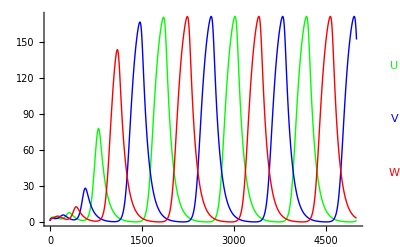

```mathematica
sim=run[r, initialConditions-> baseic, rates-> baserates, timeSpan-> 5000];
runPlot[sim]
```

### Save as CelleratorML and re-read to verify correct save

```mathematica
<<CelleratorML.m
```

Cellzilla2D (2.1.α.18 5 Sept 2009) loaded Sun 25 Oct 2009 09:48:45 using xlr8r 0.74 (13 May 2009) and xSSA 1.1.α.5 (23-Jul-2009)

CelleratorML 1.0.5 (19 June 2009) loaded 25 October 2009 at 09:48 GMT-06:60 using Mathematica Version 7.0 for Linux x86 (64-bit) (February 18, 2009) Release 1

```mathematica
SaveModel["Ring-Oscillator-Hill.xml", r, "Name"-> "Hill-Ring-Oscillator", "Parameters"-> baserates, "InitialConditions"-> baseic]
```

Ring-Oscillator-Hill.xml

```mathematica
{model,parms, ic, opts}=GetModel["Ring-Oscillator-Hill.xml"]
```

Model: Hill-Ring-Oscillator

CelleratorML Version: 1.0

6 reactions

5 parameters

3 initial values

{{{U↦V,hill[1,KH,-n,0,v]},{V↦W,hill[1,KH,-n,0,v]},{W↦U,hill[1,KH,-n,0,v]},{V⇄∅,k1,k2},{U⇄∅,k1,k2},{W⇄∅,k1,k2}},{KH→1,v→2,k1→0.01,k2→0,n→3},{U→0.9,V→1,W→1.1},{Name→Hill-Ring-Oscillator,Frozen→{}}}

```mathematica
num=run[model, initialConditions-> ic, rates-> parms, timeSpan-> 5000];
runPlot[num]
```

-Graphics-